# CCBH-Power Law + Peak-ParameterDependenceTest

Davi  C. Rodrigues (this code). Jun, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
GBH = Growing Black Hole model (w = -1, has no impact on cosmology)
m1 = primary mass of the BBH or NSBH .

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Directories.wl";

(*
  Calling wl files
  ***************** 
*)

getCode["Constants.wl"];
baseSimPoints = 10^5; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

(*getCode["ObsDataPreparationGWTC-3.wl"];*) (*Not essential for this notebook*)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
(*getCode["MassFactorCorrection.wl"];*) (*This notebook requires a modified version.*)

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

End of running wl files.

## Testing PLPP parameter dependence (using 3 10^5)

here I have to select randomly different PLPP values and find the probability with reference values.

```mathematica
(*The quantiles for GWTC-3 PLPP parameters, 5%, 16%, Median, 84%, 95%. Provided by Sumit Kumar.*)

(*
alpha = Around[#3, {#1 - #3, #5-#3 }] & @@ Evaluate@ReleaseHold[Hold[2.91368096 3.10533638 3.40401232 3.73461844 3.98690423] /. Times -> List];
beta =  Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[-0.24646612  0.23829546  1.07679192  2.04662647  2.83787879] /. Times -> List ] ;
mmax = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[77.49731724 79.92731197 86.85433456 94.93299396 98.2530281] /. Times -> List ];
mmin = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[3.55443173 4.21290074 5.08383396 5.68043848 5.95357982] /. Times -> List ];
lam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[0.01308824 0.02074258 0.03868563 0.06805879 0.09687909] /. Times -> List ];
mpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[29.93629207 31.68191701 33.72549972 35.13203767 35.98450818] /. Times -> List ];
sigpp = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.45384514 2.07879345 3.55853002 6.07252803 8.14412684] /. Times -> List ];
deltam = Around[#3, {#1 - #3, #5-#3 }]& @@ ReleaseHold[Hold[1.60127061 2.97112556 4.82841 6.8000636  8.15460135] /. Times -> List ];

alpha1 = Around[#3, {#2 - #3, #4-#3 }] & @@ Evaluate@ReleaseHold[Hold[2.91368096 3.10533638 3.40401232 3.73461844 3.98690423] /. Times -> List];
beta1 =  Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[-0.24646612  0.23829546  1.07679192  2.04662647  2.83787879] /. Times -> List ] ;
mmax1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[77.49731724 79.92731197 86.85433456 94.93299396 98.2530281] /. Times -> List ];
mmin1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[3.55443173 4.21290074 5.08383396 5.68043848 5.95357982] /. Times -> List ];
lam1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[0.01308824 0.02074258 0.03868563 0.06805879 0.09687909] /. Times -> List ];
mpp1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[29.93629207 31.68191701 33.72549972 35.13203767 35.98450818] /. Times -> List ];
sigpp1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[1.45384514 2.07879345 3.55853002 6.07252803 8.14412684] /. Times -> List ];
deltam1 = Around[#3, {#2 - #3, #4-#3 }]& @@ ReleaseHold[Hold[1.60127061 2.97112556 4.82841 6.8000636  8.15460135] /. Times -> List ];
*)
(*
  minA[around_] := around /. Around[x_, y_] :>  x - y[[1]];
  maxA[around_] := around /. Around[x_, y_] :>  x + y[[2]];
  randomPP[parameter_] := RandomVariate[UniformDistribution[{minA[parameter], maxA[parameter]}]];
*)

assoSamplesPLPPraw = Import[FileNameJoin[{pathIn, "all_samples_PLPP_GWTC3.h5"}], "Data"]; (*Data imported as association, asso for short.*)
assoSamplesPLPP = KeyMap[StringDelete[#, {"/", "_"}] & , assoSamplesPLPPraw]; (*Removes inconvenient strings from the key names.*) 

alpha = assoSamplesPLPP["alpha"];
beta = assoSamplesPLPP["beta"];
mmax = assoSamplesPLPP["mmax"];
mmin = assoSamplesPLPP["mmin"];
lam = assoSamplesPLPP["lam"];
mpp = assoSamplesPLPP["mpp"];
sigpp = assoSamplesPLPP["sigpp"];
deltam = assoSamplesPLPP["deltam"];

lengthSample = Length @ alpha;
```

Modified version of the MassFactorCorrection.wl code, to allow for parameter variation: no memory.

```mathematica
ClearAll[
  massFactorDelay, 
  dataMassFactor,
  dataDelayTime,
  minDelayTime, 
  maxDelayTime
];

Echo[baseSimPoints, "Base number of simmulated points per dimension (baseSimPoints): "];

listDelayTime = Range[tdmin0/10, tdmax0, 0.015]; (* delayTime values to be computed. tdmin lower than tdmin0 will be considered*)
listzObs = Range[0.0, 1.0, 0.01];
listw = Range[-1.5, -0.5, 0.1]; 

minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] :=  Min[
  tdmax,
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/a_i)^k. This is the factor that corrects the mass*)

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  proportionalBaseSimPoints[tdmin, tdmax]]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
 
(*
  FORMATION MASS
  ***********
*)

(* ::Section:: *)
(* Formation Mass *)

Clear[dataM1FormationRaw, dataM1Formation, dataM1Merger];

(*Options[plpp`plpp] := {
  plpp`a -> randomPP[alpha],
  plpp`mMin -> randomPP[mmin],
  plpp`dm -> randomPP[deltam],
  plpp`mMax -> randomPP[mmax],
  plpp`mu -> randomPP[mpp],
  plpp`s -> randomPP[sigpp],
  plpp`l -> randomPP[lam],
  plpp`betaQ -> randomPP[beta]
}; *)

𝒟plp := (
  random = RandomInteger[lengthSample];
  plpp`𝒟[
    plpp`a -> alpha[[random]],
    plpp`mMin -> mmin[[random]],
    plpp`dm -> deltam[[random]],
    plpp`mMax -> mmax[[random]],
    plpp`mu -> mpp[[random]],
    plpp`s -> sigpp[[random]],
    plpp`l -> lam[[random]],
    plpp`betaQ -> beta[[random]]
  ]
); (*plpp`𝒟 is defined in PowerLawPlusPeakDefinition.wl.*)

dataM1Merger := RandomVariate[𝒟plp, 2 baseSimPoints]; 
(*
  "2 baseSimPoints" is important to guarantee that the number of dataM1Merger points will be larger than the number of points 
  of dataMassFactor, which depends on tdmin, tdmax.
*)

dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= Block[
  {length, dataM1MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM1MergerSameLength = Take[dataM1Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM1MergerSameLength 
];(*Note that the k=1 inside dataMassFactor, but there is k in the exponent. It's relevant for function memmory, 
such that dataMassFactor needs not to be comptuted again if k changes.*)

dataM1Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^(2*72);
```

Base number of simmulated points per dimension (baseSimPoints):   100000

```mathematica
Table[probabilityMminApprox[2], {i, 3}] // EchoTiming
```

9.78664

{0.000456243,0.000122971,0.000206939}

```mathematica
listProbSamplePLPPv2 = Table[probabilityMminApprox[2], {i, 1000}]; // EchoTiming
Export["listProbSamplePLPPv2.csv", listProbSamplePLPPv2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {81.495}. NIntegrate obtained 167.008 and 0.000346292 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {75.7003}. NIntegrate obtained 293.018 and 0.00175369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {77.6649}. NIntegrate obtained 448.881 and 0.00535283 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
listProbSamplePLPP = Table[findSigma[probabilityMminApprox[2]], {i, 1000}]; // EchoTiming
Export["listProbSamplePLPP.csv", listProbSamplePLPP]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {74.9651}. NIntegrate obtained 636.121 and 0.0042021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {75.7341}. NIntegrate obtained 312.892 and 0.00209219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in plpp`m near {plpp`m} = {82.5573}. NIntegrate obtained 243.326 and 0.000446825 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Still waiting for a safe time to evaluate $Inspector[]

4540.78

listProbSamplePLPP.csv

```mathematica
i
```

197

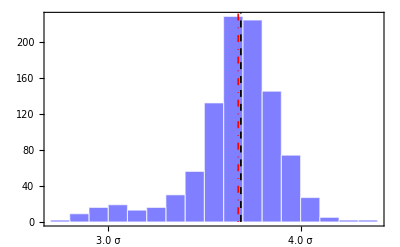

pathOut/histRandomPLPP.pdf

```mathematica
histSamplePLPP = Histogram[
  listProbSamplePLPP, 
  {0.1}, 
  Axes -> False, 
  Frame -> True , 
  Background->White, 
  ChartBaseStyle->EdgeForm[White], 
  ChartStyle->Directive[Blue, Opacity[0.5]], 
  FrameStyle-> Directive[Black, FontSize -> 13], 
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks-> {{Automatic, Automatic}, {Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style[" σ", FontFamily-> "Times"]}, {i, 1, 5, 0.2}], Automatic}},
  Epilog-> {Dashed, Black, Thickness[0.003], Line[{{Median @ listProbSamplePLPP, 0}, {Median @ listProbSamplePLPP, 1000}}], Red, DotDashed, Line[{{3.676, 0}, {3.676, 1000}}]}
]

exportOut["histRandomPLPP.pdf", histSamplePLPP]
```

```mathematica
Quantile[listProbSamplePLPP, 0.05]
Quantile[listProbSamplePLPP, 0.95]
```

3.11594

```mathematica
Median @ listProbSamplePLPP
```

3.68967

```mathematica
i
```

22

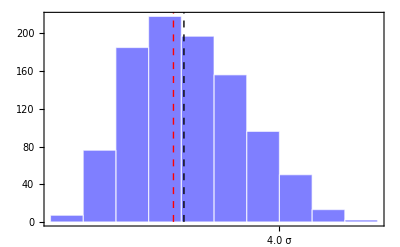

```mathematica
histRandomPLPP1 = Histogram[
  listProbRandom1, 
  {0.1}, 
  Axes -> False, 
  Frame -> True , 
  Background->White, 
  ChartBaseStyle->EdgeForm[White], 
  ChartStyle->Directive[Blue, Opacity[0.5]], 
  FrameStyle-> Directive[Black, FontSize -> 13], 
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks-> {{Automatic, Automatic}, {Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style[" σ", FontFamily-> "Times"]}, {i, 1, 5, 0.2}], Automatic}},
  Epilog-> {Dashed, Black, Line[{{Median @ listProbRandom1, 0}, {Median @ listProbRandom1, 1000}}], Red, Line[{{3.676, 0}, {3.676, 1000}}]}
]
```

```mathematica
i
```

28

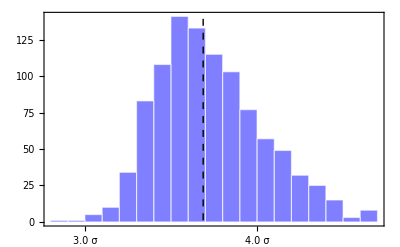

pathOut/histRandomPLPP.pdf

```mathematica
histRandomPLPP = Histogram[
  listProbRandom2, 
  {0.1}, 
  Axes -> False, 
  Frame -> True , 
  Background->White, 
  ChartBaseStyle->EdgeForm[White], 
  ChartStyle->Directive[Blue, Opacity[0.5]], 
  FrameStyle-> Directive[Black, FontSize -> 13], 
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  GridLines->{{listProbRandom2 // Median}, None},
  GridLinesStyle->Directive[Black, Dashed, Thickness[0.0025]],
  FrameTicks-> {{Automatic, Automatic}, {Table[{i, ToString@NumberForm[i, {2,1}]<>ToString@Style[" σ", FontFamily-> "Times"]}, {i, 1, 5, 0.5}], Automatic}}
]

exportOut["histRandomPLPP.pdf", histRandomPLPP]
```